# Logistic Difference Equation

Where x_n is the population at time n, and r is the growth rate
x_(n+1)=rx_n (1-x_n)
x_0= 0.5

```mathematica
Clear[x]
x[r_][0]=0.3;    
x[r_][n_]:=x[r][n]=r*x[r][n-1](1 - x[r][n-1]);
```

Calculando x_n para n={1,2,...,50} con r=3.83

```mathematica
Manipulate[ListPlot[  Table[x[r][n] , {n,1,50}] ,PlotRange->{0,1}, AxesLabel->{"n" , "X"}, PlotJoined->True], {{r,0.8,"r"},0,4.0}]
```

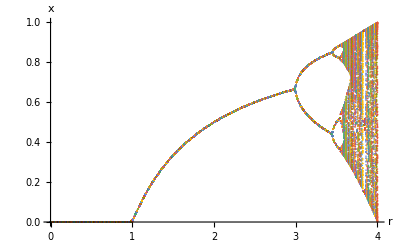

```mathematica
ListPlot[ Table[{r,x[r][n]} , {r,0, 4, 0.01}, {n, 100, 300}] , AxesLabel->{"r" , "x"}]
```